## Fermion vacuum self energy

Imaginary part:

```mathematica
(Pi*h^2)/(2*Pi)^2*1/(2*p)*Integrate[q*(HeavisideTheta[-q^2/2-ν+2μ]-HeavisideTheta[-q^2/2+ω-ν+2μ]),q]
```

(h^2 (1/2 (-q^2+2 (2 μ-ν)) HeavisideTheta[q^2/2-2 μ+ν]-1/2 (-q^2+2 (2 μ-ν+ω)) HeavisideTheta[q^2/2-2 μ+ν-ω]))/(8 p π)

```mathematica
f[q_]:=h^2/(8 p π)(1/2 (-q^2+2 (2 μ-ν)) HeavisideTheta[q^2/2-2 μ+ν]-1/2 (-q^2+2 (2 μ-ν+ω)) HeavisideTheta[q^2/2-2 μ+ν-ω])
```

```mathematica
Simplify[f[2p+Sqrt[2 p^2-2ω+2ν-2μ]]-f[2p-Sqrt[2 p^2-2ω+2ν-2μ]]]
```

1/(8 p π)h^2 ((-3 p^2+3 μ-2 ν-2 √2 p √(p^2-μ+ν-ω)+ω) HeavisideTheta[-2 μ+ν+1/2 (2 p+√(2 p^2-2 μ+2 ν-2 ω))^2]-(-3 p^2+3 μ-2 ν+2 √2 p √(p^2-μ+ν-ω)+ω) HeavisideTheta[-2 μ+ν+1/2 (-2 p+√2 √(p^2-μ+ν-ω))^2]+(-3 p^2+3 μ-2 ν+2 √2 p √(p^2-μ+ν-ω)+2 ω) HeavisideTheta[3 p^2-3 μ+2 ν-2 √2 p √(p^2-μ+ν-ω)-2 ω]+(3 p^2-3 μ+2 ν+2 √2 p √(p^2-μ+ν-ω)-2 ω) HeavisideTheta[-2 μ+ν+1/2 (2 p+√(2 p^2-2 μ+2 ν-2 ω))^2-ω])

```mathematica
SelfImFermion[h_,ω_,p_,μ_,ν_]:=1/(8 p π)h^2 ((-3 p^2+3 μ-2 ν-2 √2 p √(p^2-μ+ν-ω)+ω) HeavisideTheta[-2 μ+ν+1/2 (2 p+√(2 p^2-2 μ+2 ν-2 ω))^2]-(-3 p^2+3 μ-2 ν+2 √2 p √(p^2-μ+ν-ω)+ω) HeavisideTheta[-2 μ+ν+1/2 (-2 p+√2 √(p^2-μ+ν-ω))^2]+(-3 p^2+3 μ-2 ν+2 √2 p √(p^2-μ+ν-ω)+2 ω) HeavisideTheta[3 p^2-3 μ+2 ν-2 √2 p √(p^2-μ+ν-ω)-2 ω]+(3 p^2-3 μ+2 ν+2 √2 p √(p^2-μ+ν-ω)-2 ω) HeavisideTheta[-2 μ+ν+1/2 (2 p+√(2 p^2-2 μ+2 ν-2 ω))^2-ω])
```

Real part for p = 0:

```mathematica
Limit[SelfImFermion[h,ω,p,μ,ν],p->0]
```

(h^2 √(-μ+ν-ω) (HeavisideTheta[-3 μ+2 ν-2 ω]-HeavisideTheta[-3 μ+2 ν-ω]))/(√2 π)

```mathematica
Integrate[(h^2 √(-μ+ν-x) (HeavisideTheta[-3 μ+2 ν-2x]-HeavisideTheta[-3 μ+2 ν-x]))/(√2 π)/(x-ω)/Pi,x]
```

1/(√2 π^2)h^2 (-2 (√(2 μ-ν)-√(-x-μ+ν)-√(μ-ν+ω) ArcTan[(√(2 μ-ν))/(√(μ-ν+ω))]+√(μ-ν+ω) ArcTan[(√(-x-μ+ν))/(√(μ-ν+ω))]) HeavisideTheta[x+3 μ-2 ν]+(√2 √μ-2 √(-x-μ+ν)-2 √(μ-ν+ω) ArcTan[(√μ)/(√2 √(μ-ν+ω))]+2 √(μ-ν+ω) ArcTan[(√(-x-μ+ν))/(√(μ-ν+ω))]) HeavisideTheta[2 x+3 μ-2 ν])

```mathematica
Limit[1/(√2 π^2)h^2 (-2 (√(2 μ-ν)-√(-x-μ+ν)-√(μ-ν+ω) ArcTan[(√(2 μ-ν))/(√(μ-ν+ω))]+√(μ-ν+ω) ArcTan[(√(-x-μ+ν))/(√(μ-ν+ω))]) HeavisideTheta[x+3 μ-2 ν]+(√2 √μ-2 √(-x-μ+ν)-2 √(μ-ν+ω) ArcTan[(√μ)/(√2 √(μ-ν+ω))]+2 √(μ-ν+ω) ArcTan[(√(-x-μ+ν))/(√(μ-ν+ω))]) HeavisideTheta[2 x+3 μ-2 ν]),x->-μ+ν]
```

(h^2 ((√2 √μ-2 √(μ-ν+ω) ArcTan[(√μ)/(√2 √(μ-ν+ω))]) HeavisideTheta[μ]-2 (√(2 μ-ν)-√(μ-ν+ω) ArcTan[(√(2 μ-ν))/(√(μ-ν+ω))]) HeavisideTheta[2 μ-ν]))/(√2 π^2)

```mathematica
SelfReFermion0[h_,ω_,μ_,ν_]:=Re[(h^2 ((√2 √μ-2 √(μ-ν+ω) ArcTan[(√μ)/(√2 √(μ-ν+ω))]) HeavisideTheta[μ]-2 (√(2 μ-ν)-√(μ-ν+ω) ArcTan[(√(2 μ-ν))/(√(μ-ν+ω))]) HeavisideTheta[2 μ-ν]))/(√2 π^2)]
```

Real part for p != 0:

Every Theta function has to fulfill ω < p^2-μ+ν.
So for 0 < -2 μ +ν and μ < 0, all Theta functions are unity!
Try also without simplify and integrate...

Investigate the Heaviside Theta functions:

```mathematica
Solve[-2 μ+ν+1/2 (2 p-√(2 p^2-2 μ+2 ν-2 ω))^2==0,ω]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→-p^2-3 μ+2 ν-2 √2 √(2 p^2 μ-p^2 ν)},{ω→-p^2-3 μ+2 ν+2 √2 √(2 p^2 μ-p^2 ν)}}

```mathematica
Solve[-2 μ+ν+1/2 (2 p-√(2 p^2-2 μ+2 ν-2 ω))^2-ω==0,ω]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→1/2 (p^2-2 p √μ-3 μ+2 ν)},{ω→1/2 (p^2+2 p √μ-3 μ+2 ν)}}

```mathematica
Solve[-2 μ+ν+1/2 (2 p+√(2 p^2-2 μ+2 ν-2 ω))^2==0,ω]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→-p^2-3 μ+2 ν-2 √2 √(2 p^2 μ-p^2 ν)},{ω→-p^2-3 μ+2 ν+2 √2 √(2 p^2 μ-p^2 ν)}}

```mathematica
Solve[-2 μ+ν+1/2 (2 p+√(2 p^2-2 μ+2 ν-2 ω))^2-ω==0,ω]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→1/2 (p^2-2 p √μ-3 μ+2 ν)},{ω→1/2 (p^2+2 p √μ-3 μ+2 ν)}}

## Boson vacuum self energy

Imaginary part:

```mathematica
(Pi*h^2)/(2*Pi)^2*1/(2*p)*Integrate[q*(1-HeavisideTheta[-q^2+μ]-HeavisideTheta[-ω+q^2-μ]),q]
```

(h^2 (-1/2 (-q^2+μ) HeavisideTheta[q^2-μ]-1/2 (q^2-μ-ω) HeavisideTheta[q^2-μ-ω]))/(8 p π)

```mathematica
g[q_]:=(h^2 (-1/2 (-q^2+μ) HeavisideTheta[q^2-μ]-1/2 (q^2-μ-ω) HeavisideTheta[q^2-μ-ω]))/(8 p π)
```

```mathematica
Simplify[g[p/2+Sqrt[-p^2+2ω+4μ]/2]-g[p/2-Sqrt[-p^2+2ω+4μ]/2]]
```

1/(32 p π)h^2 ((-ω+p √(-p^2+4 μ+2 ω)) HeavisideTheta[1/2 (ω-p √(-p^2+4 μ+2 ω))]-(ω+p √(-p^2+4 μ+2 ω)) HeavisideTheta[-ω/2-1/2 p √(-p^2+4 μ+2 ω)]+ω HeavisideTheta[1/2 (-ω+p √(-p^2+4 μ+2 ω))]-p √(-p^2+4 μ+2 ω) HeavisideTheta[1/2 (-ω+p √(-p^2+4 μ+2 ω))]+ω HeavisideTheta[1/2 (ω+p √(-p^2+4 μ+2 ω))]+p √(-p^2+4 μ+2 ω) HeavisideTheta[1/2 (ω+p √(-p^2+4 μ+2 ω))])

```mathematica
SelfImBoson[h_,ω_,p_,μ_]:=1/(32 p π)h^2 ((-ω+p √(-p^2+4 μ+2 ω)) HeavisideTheta[1/2 (ω-p √(-p^2+4 μ+2 ω))]-(ω+p √(-p^2+4 μ+2 ω)) HeavisideTheta[-ω/2-1/2 p √(-p^2+4 μ+2 ω)]+(ω-p √(-p^2+4 μ+2 ω))HeavisideTheta[1/2 (-ω+p √(-p^2+4 μ+2 ω))]+(ω+p √(-p^2+4 μ+2 ω) ) HeavisideTheta[1/2 (ω+p √(-p^2+4 μ+2 ω))])
```

Real part for p = 0:

```mathematica
Limit[SelfImBoson[h,ω,p,μ],p->0]
```

-(h^2 √(μ+ω/2) (HeavisideTheta[-ω/2]-HeavisideTheta[ω/2]))/(8 π)

```mathematica
SelfImBoson0[h_,ω_,μ_]:=(h^2 √(μ+ω/2))/(8 π)
```

Real part with regularization:

```mathematica
Integrate[SelfImBoson0[h,x,μ]/(x-ω)-SelfImBoson0[h,x,μ]/(x+2μ),x]
```

(h^2 (2 μ+ω) ArcTan[(√(x+2 μ))/(√(-2 μ-ω))])/(4 √2 π √(-2 μ-ω))

For μ < 0:

```mathematica
SelfReBoson01[h_,ω_,μ_]:=-(h^2 √(-μ-ω/2))/(8 π)
```

For 0 < μ:

```mathematica
SelfReBoson02[h_,p_,ω_,μ_]:=Re[-(h^2 (√(2 μ)-√(-2 μ-ω) ArcTan[(√(2 μ))/(√(-2 μ-ω))]))/(2 √2 π^2)-(h^2 √(-μ-ω/2))/(8 π)]
```

Real part for p != 0:

Every Theta function has to fulfill p^2/2 - 2μ < ω.
So for μ < 0, all Theta functions are unity?
Not Galilei invariant?

Consider all possible combinations...
1st term:

The Theta function HeavisideTheta[1/2 (ω-p √(-p^2+4 μ+2 ω))] is only non-zero if p^2/2 - 2μ < ω < p^2-2 p √μ and p^2+2 p √μ < ω  (0<μ) and p^2/2 - 2μ < ω (μ<0):

```mathematica
Solve[(ω-p √(-p^2+4 μ+2 ω))==0,ω]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ω→p^2-2 p √μ},{ω→p^2+2 p √μ}}

```mathematica
p=1.4;μ=0.1;
```

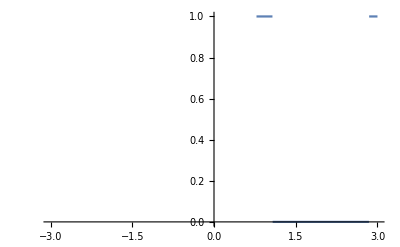

```mathematica
Plot[HeavisideTheta[1/2 (ω-p √(-p^2+4 μ+2 ω))],{ω,-3,3}]
```